```mathematica
SetDirectory[SystemDialogInput["Directory"]]
```

D:\monitorParticle

```mathematica
SetDirectory["D:\\monitorParticle\\"]
```

D:\monitorParticle

```mathematica
GetOrg[orgNo_]:=Module[{path1,path2,birth,death},
path1 = StringForm["organisms\\org``.json",orgNo]//ToString;
path2 = StringForm["orgDeaths\\org``.json",orgNo]//ToString;
birth=Import[path1];
death=Import[path2];
{("step"/.death)-("step"/.birth),"cause"/.death}
]
```

```mathematica
deadOrganisms=
StringCases[
FileNames["*","orgDeaths"],
"orgDeaths\\org"~~i:DigitCharacter..~~".json"-> i
]//Flatten;
deadOrganisms//Length
```

3109

```mathematica
{ages,deathCauses}=Transpose[ParallelMap[GetOrg,deadOrganisms]];
```

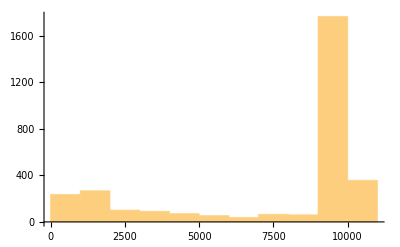

```mathematica
Histogram[ages]
```

```mathematica
tally=Tally[deathCauses];
PieChart[Apply[Labeled,Reverse[tally,2],{1}],PlotLabel->TableForm[tally]]
```

-Graphics-

```mathematica
PieChart[deathCauses]
```

-Graphics-